-Graphics3D-

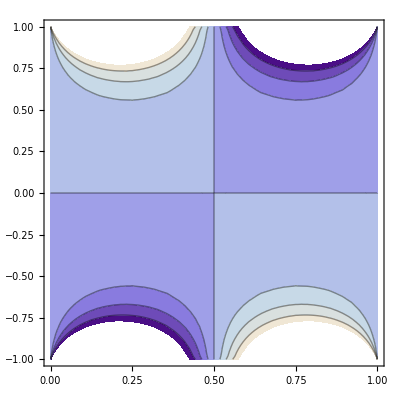

```mathematica
(*Зададим область D=[0;a]x[-b;b]*)
a=1;
b=1;
(*Зададим граничные условия*)
Phi={1-2*x,2*x-1};
Psy={y,-y};
(*Зададим количество членов в частичной сумме рядов Фурье*)
k=100;
(*Найдем коэффициенты ряда Фурье для функции u1[x,y]*)
A1[n_]=1/b*Integrate[Psy[[1]]*Cos[Pi*n*y/(2*b)],{y,-b,b}];
B1[n_]=1/Sinh[Pi*n*a/(2*b)]*(1/b*Integrate[Psy[[2]]*Cos[Pi*n*y/(2*b)],{y,-b,b}]-A1[n]*Cosh[Pi*n*a/(2*b)]);
(*Зададим функцию u1[x,y]*)
u1[x_,y_]=Sum[(A1[n]*Cosh[Pi*n*x/(2*b)+B1[n]*Sinh[Pi*n*x/(2*b)]])*Cos[Pi*n*y/(2*b)],{n,1,k}];
(*Найдем коэффициенты ряда Фурье для функции u2[x,y]*)A2[n_]=1/(2*a*Cosh[Pi*n*b/a])*Integrate[(Phi[[1]]+Phi[[2]])*Sin[Pi*n*x/a],{x,0,a}];
B2[n_]=1/(2*a*Sinh[Pi*n*b/a])*Integrate[(Phi[[1]]-Phi[[2]])*Sin[Pi*n*x/a],{x,0,a}];
(*Зададим функцию u2[x,y]*)
u2[x_,y_]=Sum[(A2[n]*Cosh[Pi*n*y/a]+B2[n]*Sinh[Pi*n*y/a])*Sin[Pi*n*x/a],{n,1,k}];
(*Построим функцию u[x,y]*)
u[x_,y_]=u1[x,y]+u2[x,y];
(*Построим график решения задачи*)
G=Plot3D[u[x,y],{x,0,a},{y,-b,b},PlotRange->All]
(*Построим линии уровня найденного решения задачи*)
GC=ContourPlot[u[x,y],{x,0,a},{y,-b,b}]
```